```mathematica
Exit
```

## Definition

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.01;u0=10^-20;δstart=10^-10;m=10;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];VCou[r_]=-α/r;V[r_]=-α/r;
```

```mathematica
?V
```

```mathematica
Plot[{-0.1/r-(0.10415223038416566 ⅇ^(-0.9990999998788636 r))/r,-α/r-(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r,-α/r},{r,0,10},PlotLegends->"Expressions"]
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_]:=
Module[{min=1.*10^-19,max=5000,wpc=50,acg=30,prc=20,sol,ef,evShifted,evnew,steps=∞,stepfraction=10^-2,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,WorkingPrecision->wpc,PrecisionGoal->prc];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.97 SetPrecision[evShifted[[n]],3],1.03 SetPrecision[evShifted[[n]],3]},WorkingPrecision->wpc,PrecisionGoal->prc,StepMonitor:>PrintTemporary[e]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
(*time1=SessionTime[];*)
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
(*time2=SessionTime[];*)
(*Print["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa,"s"];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_]:=
Module[{efunction,amplitude},efunction=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]],2];
amplitude=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
amplitude f[rr]/.efunction
]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]]
δexpminus5=δ50e[10^-5,V[r]]
δ50V=δ50[V[r]]
```

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000904222078228224798741454110591369100187217296079) is less than WorkingPrecision (50.).

-0.00090422183179239389040718734317607712974192296647679

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.284925221356624032044892471203294882847447972356) is less than WorkingPrecision (50.).

-0.27756999471845402170433888351332281826414776174295

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.059124) is less than WorkingPrecision (50.).

{0.003,-0.059055299282675533529806365996188370453349294134168}    0.232164s

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.151223) is less than WorkingPrecision (50.).

{0.01,0.15008581249193532944763182797961465722998411189738}    0.398281s

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.02671) is less than WorkingPrecision (50.).

{0.007,0.79857613130869838273829237094995417034248455748563}    0.289205s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.284925221356624032044892471203294882847447972356) is less than WorkingPrecision (50.).

{1/100000,-0.27756999471845402170433888351332281826414776174295}    0.560396s

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.16584) is less than WorkingPrecision (50.).

{0.001,0.86181924609602759533849979765332737986868893947159}    0.176125s

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.4202) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.117309) is less than WorkingPrecision (50.).

{0.03,-0.95730595107463506298779965825024594845621292580038}    0.554393s

{0.07,0.11677517001589876383015438572719258899907284648308}    0.9556762s

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.52602) is less than WorkingPrecision (50.).

{0.1,-0.99070380487621791312993730325042053199244972378824}    1.142808s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.4485) is less than WorkingPrecision (50.).

{0.3,-0.96656469254897681813179050259867280369836504494261}    2.125504s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.216209) is less than WorkingPrecision (50.).

{0.7,-0.2129313466588927882435326354829806457616128732269}    2.737936s

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.139992226505432338174002546058054635418166543) is less than WorkingPrecision (50.).

{1,-1.333789731361306426804824900213162818449066820057}    3.141235s

{-0.27756999471845402170433888351332281826414776174295,0.86181924609602759533849979765332737986868893947159,-0.059055299282675533529806365996188370453349294134168,0.79857613130869838273829237094995417034248455748563,0.15008581249193532944763182797961465722998411189738,-0.95730595107463506298779965825024594845621292580038,0.11677517001589876383015438572719258899907284648308,-0.99070380487621791312993730325042053199244972378824,-0.96656469254897681813179050259867280369836504494261,-0.2129313466588927882435326354829806457616128732269,-1.333789731361306426804824900213162818449066820057}

## Determine the best 𝒶 value (using V_eff^(a^2))

```mathematica
aa={100,10,5,1,0.5,0.1,0.05,0.01};
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[a_,c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{c1start_,c1end___}]:=Module[{aaa,findroot},aaa=a;
Print[aaa];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δexpminus10,{c1,c1start,c1end},MaxIterations->200,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a=Determinec1[#,{0}]&/@Drop[aa,0];
```

100

NDSolve::precw: The precision of the differential equation ({{20 (1.×10^-10+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0015378003046199967663261389411543694595199780115) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1.×10^-10+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0015378003046199967663261389411543694595199780115) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000-9.46129×10^-12 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00153780061101287564540899108145402666169707847452) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{-0.0308136,-0.00024468592}

{-0.0622818,-0.000067848773}

{-0.0789115,-8.3761781×10^-6}

{-0.0815797,-1.5883263×10^-7}

{-0.0816322,-5.9088965×10^-11}

{-0.08163226013749678827386387,-1.4444087×10^-17}

{-0.081632260137501572263341145471563589826292863078696,-2.766099×10^-29}

{-0.081632260137501572263341154633090259589475693324967,-2.×10^-53}

-0.081632260137501572263341154633090259589475693324967

10

{0.0230709,0.00094924595}

{0.0756524,0.00050964888}

{0.205043,0.00027583705}

{0.515455,0.00012827604}

{0.952509,0.000029525423}

{1.11102,1.1750609×10^-6}

{1.11784,1.6289177×10^-9}

{1.11785,3.1183163×10^-15}

{1.11784863358236592174907,1.535447×10^-20}

{1.1178486335823660110555051538865965097069183888853,-9.1991296×10^-34}

{1.1178486335823660110555051538812460058826075077254,0.}

1.1178486335823660110555051538812460058826075077254

5

{-0.0488532,-0.00014907573}

{-0.0899854,-0.000033461564}

{-0.105291,-2.5111243×10^-6}

{-0.106633,-1.6225226×10^-8}

{-0.106641,-6.8662136×10^-13}

{-0.1066414946738239886925137,-5.5914351×10^-20}

{-0.10664149467382401896563329502251395702584631861381,-7.1518853×10^-32}

{-0.10664149467382401896563329506123565797940770077722,0.}

-0.10664149467382401896563329506123565797940770077722

1

{-0.0703785,3.5904254×10^-7}

{-0.0692031,1.0619899×10^-10}

{-0.0692027,8.8646685×10^-18}

{-0.06920274745803390493833107,-1.2217322×10^-21}

{-0.069202747458033908940464418566394446776442584239807,1.2093663×10^-31}

{-0.069202747458033908940464418170231906820038934163707,0.}

-0.069202747458033908940464418170231906820038934163707

0.5

{-0.0672673,1.2412934×10^-7}

{-0.065899,5.3777582×10^-11}

{-0.0658984,9.8314184×10^-18}

{-0.06589837586057882220421632,-6.1233301×10^-22}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-0.06589837586057882220421632174041039837572420082821

0.1

{-0.0637854,1.4887777×10^-9}

{-0.0634271,4.7536886×10^-14}

{-0.06342706750366339101880862,-2.1289526×10^-23}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-0.063427067503663391018808619871657849577373244898379

0.05

{-0.0633088,1.9058671×10^-10}

{-0.0631284,1.5567953×10^-15}

{-0.06312835806512265213183663,-1.3367857×10^-23}

{-0.063128358065122664785267011733713315842329041144258,9.7018792×10^-24}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-0.063128358065122664785267011733713315842329041144509

0.01

{-0.0629268,1.5325549×10^-12}

{-0.062891,4.9536035×10^-19}

{-0.062890978608620453504715,-2.5098316×10^-23}

{-0.062890978608621040728765491471589770678592598518439,1.3088845×10^-23}

-0.062890978608621040728765491471589770678592598518778

```mathematica
Module[{aaa,findroot,Solveδ,hhhc1δ,evnhhhc1δ},aaa=aa[[7]];
Solveδ[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
Print["Start"];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
(*Print[sol];*)
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->20,PrecisionGoal->15];
Print[δs];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
];
hhhc1δ[en_,a_,c1_?NumberQ]:=Solveδ[en,Vs1[r,a,c1]];
evnhhhc1δ[a_,c1_]:=N[hhhc1δ[10^-10,a,c1]-δexpminus10,8];
Print[aaa];findroot=FindRoot[hhhc1δ[10^-10,aaa,c1]==δexpminus10,{c1,-0},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30,StepMonitor:>Print[{c1,evnhhhc1δ[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a
```

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)}];
Δa=Abs[δa[[#]]-δ50V]&/@Range@Length[aa];
La=Transpose@({Drop[ee,1]}~Join~{Δa[[#]]})&/@Range@Length[aa];
```

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.278660926445452816438000692556932605262991888395) is less than WorkingPrecision (50.).

{1/100000,-0.27176654934069239460746616118363673983636892440588}    0.12709s

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.93127) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-31.8042) is less than WorkingPrecision (50.).

{0.003,-0.74982493467500865161493104162736785726600748640828}    0.390276s

{0.001,-1.539364332313772880403490694404281484481089579862}    0.2812s

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.703048) is less than WorkingPrecision (50.).

{0.01,-0.61276836259346038086249967088134517093723920993978}    0.7525327s

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.395238) is less than WorkingPrecision (50.).

{0.007,0.37639442515159482246914250005424491534424798583827}    0.615436s

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0198909) is less than WorkingPrecision (50.).

{0.07,-0.019888320936434816305436796050027975563693067032914}    2.052452s

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.23265) is less than WorkingPrecision (50.).

{0.03,0.88922806126838197769409379705269591917632670371877}    1.392985s

NDSolve::precw: The precision of the differential equation ({{20 (1+0.000051831290056597765178778837780065358044407293258487 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==6.59561) is less than WorkingPrecision (50.).

{0.1,1.420326286291809673373564873410658046575040256647}    2.740936s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.69387) is less than WorkingPrecision (50.).

{0.3,-1.0374910799452267509322674144076406839465728713143}    4.111908s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.587001) is less than WorkingPrecision (50.).

{0.7,-0.53080642735344086178614939827593075610311833802607}    5.459862s

FindRoot::precw: The precision of the argument function (Tan[δ]==-5.6788243823823451178956959795792569582227658444) is less than WorkingPrecision (50.).

{1,-1.3964905447065031729490167856804617613775267813705}    6.767787s

NDSolve::precw: The precision of the differential equation ({{20 (1/100000-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.746461) is less than WorkingPrecision (50.).

{0.003,-0.64123205966443987338991228536050980416287296779165}    0.7435265s

NDSolve::precw: The precision of the differential equation ({{20 (0.007-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.286070419679675743477917209143138669025048125181) is less than WorkingPrecision (50.).

{1/100000,-0.27862888395226276435703887047387412182250463240135}    0.8425955s

NDSolve::precw: The precision of the differential equation ({{20 (0.001-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==4.2736) is less than WorkingPrecision (50.).

{0.01,1.340937437079892031329774510241584464236652077954}    1.387981s

NDSolve::precw: The precision of the differential equation ({{20 (0.03-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.741096) is less than WorkingPrecision (50.).

{0.001,0.63777799320324395132028164325503626333898945751525}    0.9126583s

NDSolve::precw: The precision of the differential equation ({{20 (0.1-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.786489) is less than WorkingPrecision (50.).

{0.007,0.66644783716514787645401883991790864962087818189687}    1.31693s

NDSolve::precw: The precision of the differential equation ({{20 (0.3-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.377484) is less than WorkingPrecision (50.).

{0.03,0.36094662359708039131047691232866769061467934203387}    3.713627s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.442141) is less than WorkingPrecision (50.).

{0.07,-0.41629884906266628032402700846999377352017689960503}    5.138635s

NDSolve::precw: The precision of the differential equation ({{20 (0.7-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1-0.0070976274170267481454044209202661386000689470710179 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.210931) is less than WorkingPrecision (50.).

{0.1,0.20788360969931736755083285158772808949460908668072}    6.097312s

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.14865) is less than WorkingPrecision (50.).

{0.3,-1.1352023374949081720019355707034863812155653475815}    10.419369s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.98637) is less than WorkingPrecision (50.).

{0.7,-1.1044080262115827868022891419628949230518264066301}    13.728711s

FindRoot::precw: The precision of the argument function (Tan[δ]==-9.0691855529612240729842431840762378029191687585) is less than WorkingPrecision (50.).

{1,-1.460976473099081350717798321415709862276220901182}    16.260514s

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.285052380211396175031532810994422840728040559613) is less than WorkingPrecision (50.).

{1/100000,-0.27768760169701716331674172794616721510699816364129}    0.502356s

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.215839) is less than WorkingPrecision (50.).

{0.003,-0.21257777297710147693979227031223627498672154017919}    1.1308s

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.11822) is less than WorkingPrecision (50.).

{0.001,0.84115109166929819561351896203605893189231647144822}    0.93166s

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.129756) is less than WorkingPrecision (50.).

{0.01,-0.12903541823393597565301971887731908450122721156502}    1.752242s

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.826698) is less than WorkingPrecision (50.).

{0.007,0.69080982837426197516553324581265558804575067488384}    1.385981s

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-7.15809) is less than WorkingPrecision (50.).

{0.03,-1.431992509128479245223122183003885145240852209855}    3.489467s

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0738111) is less than WorkingPrecision (50.).

{0.07,0.073677485043801290836523867511276112591053328581832}    5.474872s

NDSolve::precw: The precision of the differential equation ({{20 (1+0.0013542112476606159435827323384932744831450009476012 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.43119) is less than WorkingPrecision (50.).

{0.1,-1.1805687206206625716012804394046211104703323855842}    6.652705s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.5467) is less than WorkingPrecision (50.).

{0.3,-0.99685779638617797642450097468370726735305209459731}    12.18862s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.35754) is less than WorkingPrecision (50.).

{0.7,-0.34337623986232999058582745909576503559311930267575}    15.239793s

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.7950315486910033834878345885416707770557295655) is less than WorkingPrecision (50.).

{1,-1.365194058028614754870789021883502784470036505353}    19.702949s

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.284925852827390576887799898556145381612167511456) is less than WorkingPrecision (50.).

{1/100000,-0.27757057877408802992295809951351198985769961682186}    0.7535332s

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.061318) is less than WorkingPrecision (50.).

{0.003,-0.061241275110618864692330987869249564405099896593541}    1.123802s

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.139167) is less than WorkingPrecision (50.).

{0.01,0.13827878791358764626404688723960002238056140050873}    1.240885s

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.1655) is less than WorkingPrecision (50.).

{0.001,0.86167548999632335316087416100018618002881636093612}    0.7535393s

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.0205) is less than WorkingPrecision (50.).

{0.007,0.79554540179985059787028685003242909388724504693611}    0.9997065s

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.57503) is less than WorkingPrecision (50.).

{0.03,-1.005103527923773304303003606735657631061624700773}    2.273608s

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.107782) is less than WorkingPrecision (50.).

{0.07,0.10736738375919643318714349487170045466464642414777}    4.067884s

NDSolve::precw: The precision of the differential equation ({{20 (1+0.004393934052749624728921949974367019999430772381302 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.69322) is less than WorkingPrecision (50.).

{0.1,-1.0373236725086005228655689005225927617840761301298}    4.076884s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.49046) is less than WorkingPrecision (50.).

{0.3,-0.97984422855719818086190857160077014388360040201625}    6.82783s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.284696) is less than WorkingPrecision (50.).

{0.7,-0.27735794297891748348484062580889955407272423244762}    9.6918559s

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.4835889582240297605756460044407743303561941547) is less than WorkingPrecision (50.).

{1,-1.351352403493578343928637819941601574940646835042}    11.784337s

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.284925266115390084391418191666977353585280431096) is less than WorkingPrecision (50.).

{1/100000,-0.27757003611643301145601106906723712139542688212642}    0.465315s

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0592863) is less than WorkingPrecision (50.).

{0.003,-0.059216993477974401835936589460871104554939903783092}    0.7805406s

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.16581) is less than WorkingPrecision (50.).

{0.001,0.86180891761766746066724431653985173109771654586768}    0.555393s

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.15024) is less than WorkingPrecision (50.).

{0.01,0.14912490621344305186125071982709375813639378834699}    1.362964s

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.02622) is less than WorkingPrecision (50.).

{0.007,0.79833945438936023861653414856461627727533873054475}    0.9156462s

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.115902) is less than WorkingPrecision (50.).

{0.07,0.11538749464663100868598856894960034408619283565829}    2.993116s

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.43484) is less than WorkingPrecision (50.).

{0.03,-0.96212618881336938761215726643597311501787861166324}    1.815283s

NDSolve::precw: The precision of the differential equation ({{20 (1+0.00836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.55372) is less than WorkingPrecision (50.).

{0.1,-0.99892222451595852682215664034666363188965305766815}    3.073173s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.46406) is less than WorkingPrecision (50.).

{0.3,-0.97154828427184767585361165143104509862034243765585}    5.416832s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.251559) is less than WorkingPrecision (50.).

{0.7,-0.24644581481258216115535384426038682328061819587339}    7.8495654s

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.3362229797932127121873244413970937136432279121) is less than WorkingPrecision (50.).

{1,-1.344143492015230952372341579684895100849490583741}    8.4860032s

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0591243) is less than WorkingPrecision (50.).

{0.003,-0.059055588652625450210560870178185798243878235919175}    0.614434s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.284925221435682062959707104986327680365112920676) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.27756999479157584855477149210110283948063931744789}    0.644454s

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.151221) is less than WorkingPrecision (50.).

{0.01,0.15008403964543867550448783889350112003131653914677}    0.9997072s

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.16584) is less than WorkingPrecision (50.).

{0.001,0.86181922777424569423696256438817855392642215720102}    0.618438s

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.02671) is less than WorkingPrecision (50.).

{0.007,0.79857570033281487633765435460486737979802857000801}    0.9736906s

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.117306) is less than WorkingPrecision (50.).

{0.07,0.11677190367333357419311270458191658167665265381614}    2.483756s

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.42023) is less than WorkingPrecision (50.).

{0.03,-0.9573156048157062658197555854712632255636105104594}    1.626151s

NDSolve::precw: The precision of the differential equation ({{20 (1+0.0402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.52609) is less than WorkingPrecision (50.).

{0.1,-0.99072531544744900345806925703254431093199924130954}    3.16524s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.44858) is less than WorkingPrecision (50.).

{0.3,-0.96658996513936366294547143812801014362673570109205}    4.972517s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.216625) is less than WorkingPrecision (50.).

{0.7,-0.21332865137296101142179692838835553900962882413327}    6.516622s

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.1436089466333413021588399939960444470138305594) is less than WorkingPrecision (50.).

{1,-1.333988950195271043143027378711774387165158540509}    8.2208142s

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.284925221361626097770835138858106474896306352922) is less than WorkingPrecision (50.).

{1/100000,-0.27756999472308049898541497798824905931868344371763}    0.552391s

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0591241) is less than WorkingPrecision (50.).

{0.003,-0.059055317598678517213826311752386518690200114102895}    0.609431s

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.151223) is less than WorkingPrecision (50.).

{0.01,0.15008570017237816590200491537597087663545115941178}    0.9396644s

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.16584) is less than WorkingPrecision (50.).

{0.001,0.86181924493663993000039941894595220585042455395979}    0.556394s

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.02671) is less than WorkingPrecision (50.).

{0.007,0.79857610401497691769340975696287538279442858597359}    0.7815534s

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.4202) is less than WorkingPrecision (50.).

{0.03,-0.95730656432685884728926138396103419236407713954985}    1.438017s

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.117309) is less than WorkingPrecision (50.).

{0.07,0.11677496141170695201587556104139205423236174461935}    2.449746s

NDSolve::precw: The precision of the differential equation ({{20 (1+0.080165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.52602) is less than WorkingPrecision (50.).

{0.1,-0.99070518411125325102274783154031556086827426392382}    2.708917s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.44851) is less than WorkingPrecision (50.).

{0.3,-0.96656635645096810220668903792213562577994768026912}    4.874449s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.216238) is less than WorkingPrecision (50.).

{0.7,-0.21295888777845605893328052046284717058406150060152}    6.536623s

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.1402526137461462160344688397957681767591406447) is less than WorkingPrecision (50.).

{1,-1.333804085188906256596860857115341253768599963066}    7.7264646s

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.059124) is less than WorkingPrecision (50.).

{0.003,-0.059055299312273166225838935494857508645309281086594}    1.394986s

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.284925221356632114074868189016752406656093753889) is less than WorkingPrecision (50.).

{1/100000,-0.27756999471846149688161889357261331547832514109403}    1.610137s

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.151223) is less than WorkingPrecision (50.).

{0.01,0.15008581231037851587782175791115762709650396903417}    2.239584s

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.16584) is less than WorkingPrecision (50.).

{0.001,0.86181924609415414860546889077406913370505980450345}    1.141808s

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.02671) is less than WorkingPrecision (50.).

{0.007,0.79857613126458558816709627443332600228154777420054}    2.196553s

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.117309) is less than WorkingPrecision (50.).

{0.07,0.11677516967783933071483804897877448265890287421178}    6.536624s

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.4202) is less than WorkingPrecision (50.).

{0.03,-0.95730595206676200529884387032493838448792229426662}    5.362794s

NDSolve::precw: The precision of the differential equation ({{20 (1+0.399318 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.52602) is less than WorkingPrecision (50.).

{0.1,-0.99070380711423713476188149526299316808889194040762}    8.3879306s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.4485) is less than WorkingPrecision (50.).

{0.3,-0.9665646952720327634265517044879344217650636303293}    13.739718s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.216209) is less than WorkingPrecision (50.).

{0.7,-0.21293139250220302115927203603386346034911288364047}    20.262329s

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.1399926654558029471039739264490631792020314873) is less than WorkingPrecision (50.).

{1,-1.333789755559849071658314666243310525237873538046}    23.389544s

```mathematica
Get["C:\\Users\\ASUS\\Documents\\CoulombPotential_"<>"Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".ex"]
```

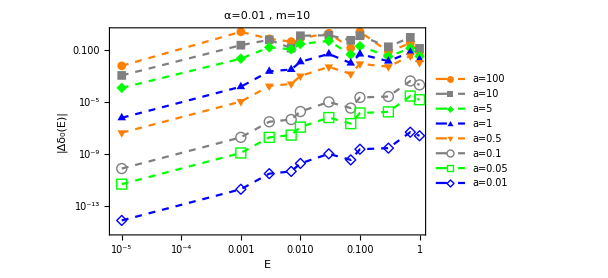

C:\Users\ASUS\OneDrive\Documents\Test_6\Test_Determine_Coulomb_a_Alpha=0.01&m=10.eps

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\CoulombPotential_"<>"Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".ex",La];
ListLogLogPlot[Table[La[[n]],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->450,FrameLabel->{"E","|Δδ_0(E)|"},(*RotateLabel->False,*)PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}(*,{Orange},{Gray},{Green},{Blue}*)},PlotLegends->Placed[LineLegend[(("a="<>ToString[#])&/@aa),LegendLayout->{"Column",2}(*,LegendMarkerSize->20*),LegendMargins->{{0,0},{0,0}}(*,LegendFunction->Framed*)],(*{{},{}}*){Right,Bottom}],PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),18],FrameTicksStyle->{Bold,12}]
Evaluate["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Test_Determine_Coulomb_a_Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".eps"]
Export[%,%%];
```

```mathematica
LineLegend[Flatten@{{Orange},{Gray},{Green},{Blue},{Orange},{Gray},{Green},{Blue}},(("a="<>ToString[#])&/@aa),LegendLayout->Grid[{{#[[1]]},Take[#,{2,4}],Take[#,{5,8}]}]&(*,LegendMarkerSize->20*),LegendMargins->{{0,0},{0,0}}(*,LegendFunction->Framed*)]
```

LineLegend[{RGBColor[1, 0.5, 0],GrayLevel[0.5],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0.5],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{a=100,a=10,a=5,a=1,a=0.5,a=0.1,a=0.05,a=0.01},LegendLayout→Grid[{{#1⟦1⟧},Take[#1,{2,4}],Take[#1,{5,8}]}]&,LegendMargins→{{0,0},{0,0}}]